The following function generates the ‘empty’ grid with only the boundary cells filled in. Internal cells carry the value -1.

```mathematica
initialGridBorder[n_] := initialGridBorder[n] = SparseArray[{{i_, j_} /; i == 1 || j == 1 -> i + j - 2, {i_, j_} /; i == n || j == n -> 2n - i - j}, {n, n}, -1]
```

The following shows an example of a 9 x 9 boundary grid:

```mathematica
MatrixForm[initialGridBorder[9]]
```

(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 7
2 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 6
3 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 5
4 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 4
5 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 3
6 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 2
7 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1
8 | 7 | 6 | 5 | 4 | 3 | 2 | 1 | 0)

Drag the slider to see larger grids.

```mathematica
colorRules={0->Red,1->Yellow,2->Blue};
Manipulate[ArrayPlot[initialGridBorder[3(2k - 1)]],{k,1,40,1}]
```

```mathematica
(* Helper function for generateMaxHeightGrid. Fills one concentric square of cells. *)
fillConcentricSquareMax[Hold[grid_], k_] := (
 grid[[k, k ;; -k]] = grid[[k - 1, k ;; -k]] + 1; 
 grid[[-k, k ;; -k]] = grid[[-(k - 1), k ;; -k]] + 1;
 grid[[k ;; -k, k]] = grid[[k ;; -k, k - 1]] + 1; 
 grid[[k ;; -k, -k]] = grid[[k ;; -k, -(k - 1)]] + 1; 
ReleaseHold[Hold[grid]])

(* Helper function for generateMinHeightGrid. Fills one concentric square of cells. *)
fillConcentricSquareMin[Hold[grid_], k_] := (
 grid[[k, k ;; -k]] = grid[[k - 1, k ;; -k]] - 1; 
 grid[[-k, k ;; -k]] = grid[[-(k - 1), k ;; -k]] - 1;
 grid[[k ;; -k, k]] = grid[[k ;; -k, k - 1]] - 1; 
 grid[[k ;; -k, -k]] = grid[[k ;; -k, -(k - 1)]] - 1; 
ReleaseHold[Hold[grid]])

(* Generates the grid with maximum height by starting from the boundary and moving inwards, filling in concentric squares. *)
generateMaxHeightGrid[dim_] := generateMaxHeightGrid[dim] = Module[{k = 1, depth = (dim + 1) / 2},
 Nest[( k++; currGrid = #; fillConcentricSquareMax[Hold[currGrid], k]; initialGrid = currGrid ) &, initialGrid = initialGridBorder[dim], depth - 1];
 Normal[initialGrid]
]

(* Generates the grid with minimum height by starting from the boundary and moving inwards, filling in concentric squares. *)
generateMinHeightGrid[dim_] := generateMinHeightGrid[dim] = Module[{k = 1, depth = (dim + 1) / 2},
 Nest[( k++; currGrid = #; fillConcentricSquareMin[Hold[currGrid], k]; initialGrid = currGrid ) &, initialGrid = initialGridBorder[dim], depth - 1];
 Normal[initialGrid]
]

(* Takes a grid with a filled in height function as input and converts it to its corresponding 3-colouring form. *)
to3Colouring[grid_] := Mod[grid, 3]

findListHeight[first_, list_, len_] := Module[{initialList = SparseArray[{}, {len}, -1], k = 0, prev = first}, (* remember that list is of length (len + 1) *)
 Nest[(k++; newList = #; prev = If[MemberQ[list[[{k, k + 1}]], 1], prev + list[[k + 1]] - list[[k]], If[list[[k]] == 2, prev + 1, prev - 1]]; newList[[k]] = prev; newList ) & , initialList, len]
] col

(* Takes a 3-coloured grid as input and returns the corresponding grid labelled with its height values. *)
(* Note: this starts with the initial border grid *)
toHeightFunction[grid_, dim_] := Module[{heightGrid = initialGridBorder[dim], k = 1},
Nest[(k++; nextHeightGrid = #; nextHeightGrid[[k, 2 ;; -2]] = findListHeight[heightGrid[[k, 1]], Normal[grid[[k, 1 ;; -2]]], dim - 2]; nextHeightGrid) &, heightGrid, dim - 2] 
]
```

See the max height grids and their corresponding 3-colourings for different side lengths. Dark cells are the highest, while white cells are at height 0:

```mathematica
Manipulate[ArrayPlot[generateMaxHeightGrid[3(2k - 1)]],{k,1,20,1}]
Manipulate[ArrayPlot[Mod[generateMaxHeightGrid[3(2k - 1)], 3]], ColorRules -> colourRules, {k,1,20,1}]
```

Manipulate::vsform: Manipulate argument ColorRules→colourRules does not have the correct form for a variable specification.

Manipulate[ArrayPlot[Mod[generateMaxHeightGrid[3 (2 k-1)],3]],ColorRules→colourRules,{k,1,20,1}]

See the min height grids and their corresponding 3 - colourings for different side lengths . Dark cells are the highest, while white cells are at height 0 :

```mathematica
Manipulate[ArrayPlot[generateMinHeightGrid[3(2k - 1)]],{k,1,20,1}]
Manipulate[ArrayPlot[Mod[generateMinHeightGrid[3(2k - 1)], 3]],{k,1,20,1}]
```

```mathematica
selectRandomCell[dim_] := RandomChoice[Tuples[Range[2, dim - 1], 2]];
coinFlip[] := RandomChoice[{True, False}]
changeColour[grid_, pos_, newVal_] := ReplacePart[grid, pos -> newVal]

(* Check if you can pop up a cell at pos in grid. Works on both height values and 3-colourings *)
checkPopUp[grid_, pos_] := AllTrue[grid[[pos[[1]] + {-1, 1}, pos[[2]]]] ~ Join ~ grid[[pos[[1]], pos[[2]] + {-1, 1}]], Mod[grid[[Sequence @@ pos]] - #, 3] == 2 &]
(* Check if you can pop down a cell at pos in grid. Works on both height values and 3-colourings *)
checkPopDown[grid_, pos_] := AllTrue[grid[[pos[[1]] + {-1, 1}, pos[[2]]]] ~ Join ~ grid[[pos[[1]], pos[[2]] + {-1, 1}]], Mod[grid[[Sequence @@ pos]] - #, 3] == 1 &]

(* If heads, check if site can be popped up; otherwise, check if site can be popped down. *)
coinFunctionAssociation = Association[True -> checkPopUp, False -> checkPopDown];
coinSignAssociation = Association[True -> Plus, False -> Subtract];

(*  *)
oneStep[dim_, maxGrid_, minGrid_] := Module[{site = selectRandomCell[dim], coin = coinFlip[], initialGrids = {maxGrid, minGrid}, outGrids = {maxGrid, minGrid}},
 (*Print[site, coinFunctionAssociation[coin]];
 Print[MatrixForm[initialGrids[[1]]], MatrixForm[initialGrids[[2]]]];*)
 Map[If[coinFunctionAssociation[coin][initialGrids[[#]], site], 
 (outGrids[[#]] = changeColour[initialGrids[[#]], site, Mod[coinSignAssociation[coin][initialGrids[[#]][[Sequence @@ site]], 2], 3]]; 
(* Print[Mod[coinSignAssociation[coin][initialGrids[[#]][[Sequence @@ site]], 2], 3]]; 
 Print[ArrayPlot[outGrids[[#]], ColorRules->colorRules, Frame-> True]]*))] &, {1, 2}];
 
(* Print[coinFunctionAssociation[coin][maxGrid, site], coinFunctionAssociation[coin][minGrid, site]];
 Print[MatrixForm[outGrids[[1]]],MatrixForm[outGrids[[2]]]];
 Print[maxGrid == outGrids[[1]], minGrid == outGrids[[2]]];
 Print[MatrixForm[maxGrid - generateMaxHeightGrid[dim]], MatrixForm[minGrid - generateMinHeightGrid[dim]]];
 isNumericMatrix = MatrixQ[maxGrid, SymbolicQ];
 isNumericMatrix1 = MatrixQ[outGrids[[1]], SymbolicQ];
 Print[isNumericMatrix];
 Print[isNumericMatrix1];*)
 outGrids
 ]
```

```mathematica
viewChangeSteps[n_, maxGrid_, minGrid_, steps_] := (gridsList = NestList[oneStep[n, Sequence @@ #] &, {maxGrid, minGrid}, steps]; 
Manipulate[Grid[{{ArrayPlot[gridsList[[k]][[1]], ColorRules -> colourRules, Frame->True], ArrayPlot[gridsList[[k]][[2]], ColorRules -> colourRules, Frame->True]}}],{k,1,steps,1}])

checkHeightDifference[n_, maxGrid_, minGrid_] := Total[Table[Abs[maxGrid[[i, j]] - minGrid[[i, j]]], {i, 2, n - 1}, {j, 2, n - 1}], 2]

viewAfterSteps[n_, maxGrid_, minGrid_, steps_, logInterval_, prevStep_] := Module[{step = 0},
  PrintTemporary[ProgressIndicator[Dynamic[step/steps]]]; {time, finalGrids} = AbsoluteTiming[Catch[Nest[(
  If[Mod[step, logInterval] == 0 || #[[1]] == #[[2]], (Export[StringJoin[ToString[NotebookDirectory[]], "output files/coupling_", ToString[n], "/log_", ToString[step + prevStep], ".mx"], #]; 
    Print[checkHeightDifference[n, #[[1]], #[[2]]]])]; 
  If[#[[1]] == #[[2]], Throw[#]]; 
  step++; 
  oneStep[n, Sequence @@ #]) &, 
  {maxGrid, minGrid}, steps + 1]]];
  {time, step, finalGrids}
]

displayTime[time_] := DateString[time, {"Hour", ":", "Minute", ":", "Second"}]
```

```mathematica
dim = 101;
maxGrid = to3Colouring[generateMaxHeightGrid[dim]];
minGrid = to3Colouring[generateMinHeightGrid[dim]];
checkHeightDifference[dim, maxGrid, minGrid]
```

8875

```mathematica
viewChangeSteps[9, maxGrid, minGrid, 10000]
```

00:27:20

28402849 steps

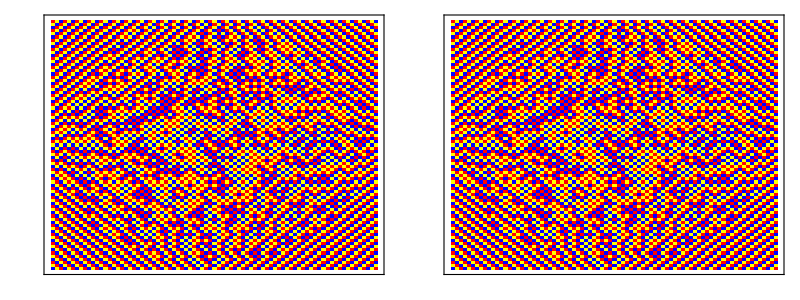

```mathematica
dim = 81;
(*grid1 = to3Colouring[generateMaxHeightGrid[dim]];
grid2 = to3Colouring[generateMinHeightGrid[dim]];*)
(* NOTE: change input and stagger! *)
{grid1, grid2} = Import[NotebookDirectory[], "output files/coupling_81/log_57000000.mx"];
{time, step, {final1, final2}} = viewAfterSteps[dim, grid1, grid2, 100000000, 1000000, 57000000];
Print[displayTime[time]];
Print[step, " steps"];
Grid[{{ArrayPlot[final1, ColorRules -> colourRules, Frame->True], ArrayPlot[final2, ColorRules -> colourRules, Frame->True]}}]
```

```mathematica
dim = 511;
grid1 = to3Colouring[generateMaxHeightGrid[dim]];
grid2 = to3Colouring[generateMinHeightGrid[dim]];
(* NOTE: change input and stagger! *)
{time, step, {final5111max, final5112min}} = viewAfterSteps[dim, grid1, grid2, 1000000000, 10000000, 0];
Print[displayTime[time]];
Print[step, " steps"];
Grid[{{ArrayPlot[final5111max, ColorRules -> colourRules, Frame->True], ArrayPlot[final5112min, ColorRules -> colourRules, Frame->True]}}]
```

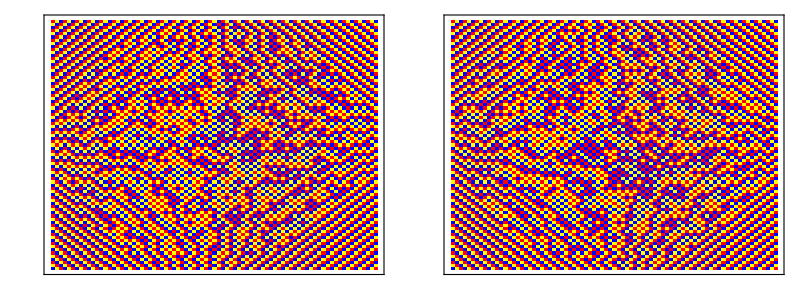

```mathematica
{final1, final2} = Import[NotebookDirectory[], "output files/coupling_81/log_57000000.mx"];
Grid[{{ArrayPlot[final1, ColorRules -> colourRules, Frame->True], ArrayPlot[final2, ColorRules -> colourRules, Frame->True]}}]
```

```mathematica
dim = 9;
maxGrid = to3Colouring[generateMaxHeightGrid[dim]];
minGrid = to3Colouring[generateMinHeightGrid[dim]];
oneStep[dim, maxGrid, minGrid]
(*MatrixForm[generateMaxHeightGrid[dim]]
MatrixForm[maxGrid]
MatrixForm[generateMinHeightGrid[dim]]
MatrixForm[minGrid]
coin = True; MatrixForm[to3Colouring[generateMinHeightGrid[dim]]]
site = {5,5};
Map[# = changeColour[#, site, Mod[coinSignAssociation[coin][#[[Sequence @@ site]], 2], 3]] &, {maxGrid, minGrid}]
Map[If[coinFunctionAssociation[coin][#, site], changeColour[#, site, Mod[coinSignAssociation[coin][#[[Sequence @@ site]], 2], 3]]] &, {maxGrid, minGrid}];
(*If[coinFunctionAssociation[coin][minGrid, site], minGrid = changeColour[minGrid, site, Mod[coinSignAssociation[coin][minGrid[[Sequence @@ site]], 2], 3]]]*)*)
(*MatrixForm[maxGrid]
MatrixForm[minGrid]*)
```

{{{0,1,2,0,1,2,0,1,2},{1,2,0,1,2,0,1,2,1},{2,0,1,2,0,1,2,1,0},{0,1,2,0,1,2,1,0,2},{1,2,0,1,2,1,0,2,1},{2,0,1,2,1,0,2,1,0},{0,1,2,1,0,2,1,0,2},{1,2,1,0,2,1,0,2,1},{2,1,0,2,1,0,2,1,0}},{{0,1,2,0,1,2,0,1,2},{1,0,1,2,0,1,2,0,1},{2,1,0,1,2,0,1,2,0},{0,2,1,0,1,2,0,1,2},{1,0,2,1,0,1,2,0,1},{2,1,0,2,1,0,1,2,0},{0,2,1,0,2,1,0,1,2},{1,0,2,1,0,2,1,0,1},{2,1,0,2,1,0,2,1,0}}}

(0 | 1 | 2 | 0 | 1 | 2 | 0 | 1 | 2
1 | 2 | 0 | 1 | 2 | 0 | 1 | 2 | 1
2 | 0 | 1 | 2 | 0 | 1 | 2 | 1 | 0
0 | 1 | 2 | 0 | 1 | 2 | 1 | 0 | 2
1 | 2 | 0 | 1 | 2 | 1 | 0 | 2 | 1
2 | 0 | 1 | 2 | 1 | 0 | 2 | 1 | 0
0 | 1 | 2 | 1 | 0 | 2 | 1 | 0 | 2
1 | 2 | 1 | 0 | 2 | 1 | 0 | 2 | 1
2 | 1 | 0 | 2 | 1 | 0 | 2 | 1 | 0)

(0 | 1 | 2 | 0 | 1 | 2 | 0 | 1 | 2
1 | 0 | 1 | 2 | 0 | 1 | 2 | 0 | 1
2 | 1 | 0 | 1 | 2 | 0 | 1 | 2 | 0
0 | 2 | 1 | 0 | 1 | 2 | 0 | 1 | 2
1 | 0 | 2 | 1 | 0 | 1 | 2 | 0 | 1
2 | 1 | 0 | 2 | 1 | 0 | 1 | 2 | 0
0 | 2 | 1 | 0 | 2 | 1 | 0 | 1 | 2
1 | 0 | 2 | 1 | 0 | 2 | 1 | 0 | 1
2 | 1 | 0 | 2 | 1 | 0 | 2 | 1 | 0)